# Tables of new LHC data

## ATLAS 7 TeV Born

```mathematica
Needs["ErrorBarLogPlots`"]
```

```mathematica
SetDirectory["PhD/newcode/data/DY.ATLAS_original"]
```

/Users/ChiaraBisso/PhD/newcode/data/DY.ATLAS_original

```mathematica
formatExport[x_]:=x//ScientificForm[#,{7,6},NumberFormat->({#1,"e",#3}&)]&//ToString//StringReplace[#,{", }"->", 0}"}]&//ToExpression//Row[{#[[1]]//ScientificForm[#,{7,6},NumberPadding->{"0","0"},SignPadding->True,NumberSigns->{"-","+"}]&,"E",#[[3]]//PaddedForm[#,2,NumberPadding->{"0","0"},SignPadding->True,NumberSigns->{"-","+"}]&}]&;
```

```mathematica
Take[ Import["DY.newATLAS_7TeV.csv","HeaderLines"->13],1]
```

{{ PT(Z) [GEV] , PT(Z) [GEV] LOW , PT(Z) [GEV] HIGH , (1/SIG(FID))*D(SIG(FID))/DPT(Z) [1/GEV] , stat + , stat - , sys,uncor + , sys,uncor - , sys,cor + , sys,cor -}}

## # : ABS (YRAP (Z)), 0.0 - 1.0

```mathematica
tableA=Take[Import["DY.newATLAS_7TeV.csv","CSV","HeaderLines"->14],26]
```

{{1.,0.,2.,0.02861,0.37,-0.37,0.34,-0.34,0.36,-0.36},{3.,2.,4.,0.05874,0.23,-0.23,0.31,-0.31,0.34,-0.34},{5.,4.,6.,0.05834,0.23,-0.23,0.23,-0.23,0.35,-0.35},{7.,6.,8.,0.04972,0.26,-0.26,0.22,-0.22,0.34,-0.34},{9.,8.,10.,0.04106,0.28,-0.28,0.24,-0.24,0.34,-0.34},{11.,10.,12.,0.03385,0.31,-0.31,0.26,-0.26,0.35,-0.35},{13.,12.,14.,0.02819,0.35,-0.35,0.27,-0.27,0.34,-0.34},{15.,14.,16.,0.02375,0.37,-0.37,0.27,-0.27,0.35,-0.35},{17.,16.,18.,0.01997,0.42,-0.42,0.29,-0.29,0.35,-0.35},{20.,18.,22.,0.01587,0.35,-0.35,0.27,-0.27,0.34,-0.34},{24.,22.,26.,0.01187,0.41,-0.41,0.29,-0.29,0.35,-0.35},{28.,26.,30.,0.009065,0.46,-0.46,0.31,-0.31,0.35,-0.35},{32.,30.,34.,0.007143,0.53,-0.53,0.35,-0.35,0.35,-0.35},{36.,34.,38.,0.005707,0.59,-0.59,0.38,-0.38,0.34,-0.34},{40.,38.,42.,0.004559,0.66,-0.66,0.44,-0.44,0.35,-0.35},{44.,42.,46.,0.003757,0.73,-0.73,0.47,-0.47,0.35,-0.35},{48.,46.,50.,0.00315,0.79,-0.79,0.48,-0.48,0.38,-0.38},{52.,50.,54.,0.002584,0.88,-0.88,0.52,-0.52,0.36,-0.36},{57.,54.,60.,0.002052,0.81,-0.81,0.48,-0.48,0.37,-0.37},{65.,60.,70.,0.001466,0.73,-0.73,0.46,-0.46,0.39,-0.39},{75.,70.,80.,0.0009646,0.92,-0.92,0.55,-0.55,0.43,-0.43},{90.,80.,100.,0.0005458,0.83,-0.83,0.53,-0.53,0.47,-0.47},{125.,100.,150.,0.0001874,0.83,-0.83,0.54,-0.54,0.57,-0.57},{175.,150.,200.,0.00004826,1.67,-1.67,0.74,-0.74,0.51,-0.51},{250.,200.,300.,0.00001126,2.38,-2.38,1.4,-1.4,1.43,-1.43},{550.,300.,800.,4.783×10^-7,5.02,-5.02,2.,-2.,1.5,-1.5}}

```mathematica
Length[tableA]
```

26

```mathematica
tableA[[All,1]]
```

{1.,3.,5.,7.,9.,11.,13.,15.,17.,20.,24.,28.,32.,36.,40.,44.,48.,52.,57.,65.,75.,90.,125.,175.,250.,550.}

```mathematica
dataA=(tableA/.{a_,b_,c_,d_,e_,f_,g_,h_,i_,l_}->{a,d,e*d/100,(√((g*d)^2+(i*d)^2))/100})
```

{{1.,0.02861,0.000105857,0.00014167},{3.,0.05874,0.000135102,0.000270268},{5.,0.05834,0.000134182,0.000244332},{7.,0.04972,0.000129272,0.000201351},{9.,0.04106,0.000114968,0.000170881},{11.,0.03385,0.000104935,0.000147588},{13.,0.02819,0.000098665,0.000122391},{15.,0.02375,0.000087875,0.000104985},{17.,0.01997,0.000083874,0.0000907702},{20.,0.01587,0.000055545,0.0000689021},{24.,0.01187,0.000048667,0.000053953},{28.,0.009065,0.000041699,0.0000423831},{32.,0.007143,0.0000378579,0.000035356},{36.,0.005707,0.0000336713,0.0000291001},{40.,0.004559,0.0000300894,0.000025632},{44.,0.003757,0.0000274261,0.0000220161},{48.,0.00315,0.000024885,0.0000192846},{52.,0.002584,0.0000227392,0.0000163427},{57.,0.002052,0.0000166212,0.0000124362},{65.,0.001466,0.0000107018,8.84109×10^-6},{75.,0.0009646,8.87432×10^-6,6.73426×10^-6},{90.,0.0005458,4.53014×10^-6,3.86633×10^-6},{125.,0.0001874,1.55542×10^-6,1.47142×10^-6},{175.,0.00004826,8.05942×10^-7,4.33723×10^-7},{250.,0.00001126,2.67988×10^-7,2.25338×10^-7},{550.,4.783×10^-7,2.40107×10^-8,1.19575×10^-8}}

```mathematica
ToPlotA=(dataA/.{a_,b_,c_,d_}->{{Log[10,a],Log[10,b]},ErrorBar[{Log[10,(b+√(c^2+d^2))/b]},{Log[10,(b-√(c^2+d^2))/b]}]})
```

{{{0.,-1.54348},ErrorBar[{0.0026763},{-0.00269289}]},{{0.477121,-1.23107},ErrorBar[{0.00222825},{-0.00223975}]},{{0.69897,-1.23403},ErrorBar[{0.00207015},{-0.00208006}]},{{0.845098,-1.30347},ErrorBar[{0.00208502},{-0.00209508}]},{{0.954243,-1.38658},ErrorBar[{0.00217296},{-0.00218389}]},{{1.04139,-1.47044},ErrorBar[{0.00231718},{-0.00232961}]},{{1.11394,-1.5499},ErrorBar[{0.00241522},{-0.00242872}]},{{1.17609,-1.62434},ErrorBar[{0.00249632},{-0.00251075}]},{{1.23045,-1.69962},ErrorBar[{0.00267944},{-0.00269607}]},{{1.30103,-1.79942},ErrorBar[{0.00241522},{-0.00242872}]},{{1.38021,-1.92555},ErrorBar[{0.00265033},{-0.00266661}]},{{1.44716,-2.04263},ErrorBar[{0.00283922},{-0.0028579}]},{{1.50515,-2.14612},ErrorBar[{0.00313809},{-0.00316093}]},{{1.5563,-2.24359},ErrorBar[{0.00337353},{-0.00339994}]},{{1.60206,-2.34113},ErrorBar[{0.00374913},{-0.00378178}]},{{1.64345,-2.42516},ErrorBar[{0.00404656},{-0.00408462}]},{{1.68124,-2.50169},ErrorBar[{0.00431901},{-0.00436239}]},{{1.716,-2.58771},ErrorBar[{0.00468112},{-0.00473213}]},{{1.75587,-2.68782},ErrorBar[{0.00437139},{-0.00441584}]},{{1.81291,-2.83387},ErrorBar[{0.00409294},{-0.00413188}]},{{1.87506,-3.01565},ErrorBar[{0.00498694},{-0.00504487}]},{{1.95424,-3.26297},ErrorBar[{0.00471332},{-0.00476503}]},{{2.09691,-3.72723},ErrorBar[{0.00493386},{-0.00499056}]},{{2.24304,-4.31641},ErrorBar[{0.00815914},{-0.00831537}]},{{2.39794,-4.94846},ErrorBar[{0.0132989},{-0.013719}]},{{2.74036,-6.3203},ErrorBar[{0.0236971},{-0.0250651}]}}

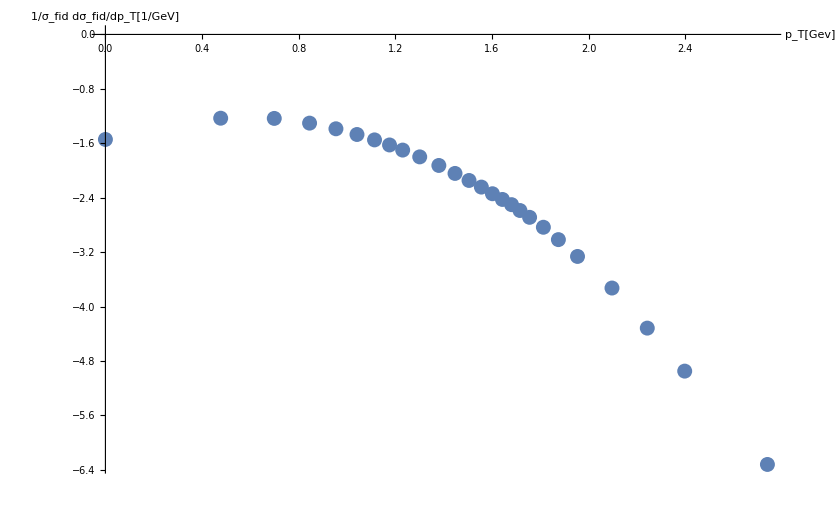

```mathematica
ErrorListPlot[ToPlotA,AxesLabel->{"p_T[Gev]", "1/σ_fid dσ_fid/dp_T[1/GeV]"},PlotRange -> All, LabelStyle->Directive[Black,FontFamily->"Helvetica",10]]
```

```mathematica
dataAExport= Table[formatExport[dataA[[k,i]]]//ToString,{k,1,26},{i,1,4}]
```

{{+1.000000E+00,+2.861000E-02,+1.058570E-04,+1.416701E-04},{+3.000000E+00,+5.874000E-02,+1.351020E-04,+2.702678E-04},{+5.000000E+00,+5.834000E-02,+1.341820E-04,+2.443325E-04},{+7.000000E+00,+4.972000E-02,+1.292720E-04,+2.013507E-04},{+9.000000E+00,+4.106000E-02,+1.149680E-04,+1.708807E-04},{+1.100000E+01,+3.385000E-02,+1.049350E-04,+1.475876E-04},{+1.300000E+01,+2.819000E-02,+9.866500E-05,+1.223914E-04},{+1.500000E+01,+2.375000E-02,+8.787500E-05,+1.049847E-04},{+1.700000E+01,+1.997000E-02,+8.387400E-05,+9.077019E-05},{+2.000000E+01,+1.587000E-02,+5.554500E-05,+6.890212E-05},{+2.400000E+01,+1.187000E-02,+4.866700E-05,+5.395303E-05},{+2.800000E+01,+9.065000E-03,+4.169900E-05,+4.238312E-05},{+3.200000E+01,+7.143000E-03,+3.785790E-05,+3.535605E-05},{+3.600000E+01,+5.707000E-03,+3.367130E-05,+2.910010E-05},{+4.000000E+01,+4.559000E-03,+3.008940E-05,+2.563196E-05},{+4.400000E+01,+3.757000E-03,+2.742610E-05,+2.201615E-05},{+4.800000E+01,+3.150000E-03,+2.488500E-05,+1.928459E-05},{+5.200000E+01,+2.584000E-03,+2.273920E-05,+1.634265E-05},{+5.700000E+01,+2.052000E-03,+1.662120E-05,+1.243620E-05},{+6.500000E+01,+1.466000E-03,+1.070180E-05,+8.841086E-06},{+7.500000E+01,+9.646000E-04,+8.874320E-06,+6.734262E-06},{+9.000000E+01,+5.458000E-04,+4.530140E-06,+3.866329E-06},{+1.250000E+02,+1.874000E-04,+1.555420E-06,+1.471418E-06},{+1.750000E+02,+4.826000E-05,+8.059420E-07,+4.337229E-07},{+2.500000E+02,+1.126000E-05,+2.679880E-07,+2.253379E-07},{+5.500000E+02,+4.783000E-07,+2.401066E-08,+1.195750E-08}}

```mathematica
Export["DY.newATLAS_7TeV_yrap01.list",dataAExport,"table"]
```

DY.newATLAS_7TeV_yrap01.list

## # : ABS (YRAP (Z)), 1.0 - 2.0

```mathematica
tableB=Take[ Import["DY.newATLAS_7TeV.csv","CSV","HeaderLines"->78],26]
```

{{1.,0.,2.,0.02781,0.42,-0.42,0.48,-0.48,0.37,-0.37},{3.,2.,4.,0.05802,0.26,-0.26,0.39,-0.39,0.35,-0.35},{5.,4.,6.,0.05782,0.25,-0.25,0.27,-0.27,0.39,-0.39},{7.,6.,8.,0.04868,0.28,-0.28,0.27,-0.27,0.38,-0.38},{9.,8.,10.,0.04047,0.31,-0.31,0.3,-0.3,0.34,-0.34},{11.,10.,12.,0.03381,0.34,-0.34,0.32,-0.32,0.34,-0.34},{13.,12.,14.,0.02823,0.38,-0.38,0.32,-0.32,0.35,-0.35},{15.,14.,16.,0.02385,0.4,-0.4,0.32,-0.32,0.34,-0.34},{17.,16.,18.,0.02034,0.44,-0.44,0.35,-0.35,0.35,-0.35},{20.,18.,22.,0.01606,0.39,-0.39,0.32,-0.32,0.35,-0.35},{24.,22.,26.,0.01217,0.47,-0.47,0.36,-0.36,0.36,-0.36},{28.,26.,30.,0.009275,0.52,-0.52,0.41,-0.41,0.35,-0.35},{32.,30.,34.,0.007339,0.59,-0.59,0.46,-0.46,0.35,-0.35},{36.,34.,38.,0.00588,0.66,-0.66,0.49,-0.49,0.35,-0.35},{40.,38.,42.,0.004709,0.74,-0.74,0.51,-0.51,0.35,-0.35},{44.,42.,46.,0.003745,0.82,-0.82,0.57,-0.57,0.38,-0.38},{48.,46.,50.,0.003156,0.86,-0.86,0.62,-0.62,0.37,-0.37},{52.,50.,54.,0.002568,0.99,-0.99,0.67,-0.67,0.36,-0.36},{57.,54.,60.,0.002125,0.92,-0.92,0.59,-0.59,0.35,-0.35},{65.,60.,70.,0.001494,0.87,-0.87,0.64,-0.64,0.39,-0.39},{75.,70.,80.,0.0009979,1.08,-1.08,0.71,-0.71,0.4,-0.4},{90.,80.,100.,0.0005566,0.99,-0.99,0.69,-0.69,0.48,-0.48},{125.,100.,150.,0.0001974,1.,-1.,0.7,-0.7,0.71,-0.71},{175.,150.,200.,0.0000499,2.03,-2.03,0.99,-0.99,0.69,-0.69},{250.,200.,300.,0.00001018,3.17,-3.17,2.05,-2.05,1.2,-1.2},{550.,300.,800.,3.048×10^-7,8.02,-8.02,3.67,-3.67,1.03,-1.03}}

```mathematica
dataB=(tableB/.{a_,b_,c_,d_,e_,f_,g_,h_,i_,l_}->{a,d,e*d/100,(√((g*d)^2+(i*d)^2))/100})
```

{{1.,0.02781,0.000116802,0.000168543},{3.,0.05802,0.000150852,0.000304038},{5.,0.05782,0.00014455,0.000274264},{7.,0.04868,0.000136304,0.000226924},{9.,0.04047,0.000125457,0.000183504},{11.,0.03381,0.000114954,0.00015786},{13.,0.02823,0.000107274,0.000133877},{15.,0.02385,0.0000954,0.000111357},{17.,0.02034,0.000089496,0.000100678},{20.,0.01606,0.000062634,0.0000761623},{24.,0.01217,0.000057199,0.0000619595},{28.,0.009275,0.00004823,0.000049999},{32.,0.007339,0.0000433001,0.0000424204},{36.,0.00588,0.000038808,0.0000354072},{40.,0.004709,0.0000348466,0.0000291274},{44.,0.003745,0.000030709,0.0000256553},{48.,0.003156,0.0000271416,0.0000227867},{52.,0.002568,0.0000254232,0.000019532},{57.,0.002125,0.00001955,0.0000145776},{65.,0.001494,0.0000129978,0.000011197},{75.,0.0009979,0.0000107773,8.13212×10^-6},{90.,0.0005566,5.51034×10^-6,4.67842×10^-6},{125.,0.0001974,1.974×10^-6,1.96817×10^-6},{175.,0.0000499,1.01297×10^-6,6.02159×10^-7},{250.,0.00001018,3.22706×10^-7,2.41815×10^-7},{550.,3.048×10^-7,2.4445×10^-8,1.16184×10^-8}}

```mathematica
ToPlotB=(dataB/.{a_,b_,c_,d_}->{{Log[10,a],Log[10,b]},ErrorBar[{Log[10,(b+√(c^2+d^2))/b]},{Log[10,(b-√(c^2+d^2))/b]}]})
```

{{{0.,-1.5558},ErrorBar[{0.00319057},{-0.00321418}]},{{0.477121,-1.23642},ErrorBar[{0.00253313},{-0.00254799}]},{{0.69897,-1.23792},ErrorBar[{0.00232242},{-0.00233491}]},{{0.845098,-1.31265},ErrorBar[{0.00235522},{-0.00236806}]},{{0.954243,-1.39287},ErrorBar[{0.00237893},{-0.00239203}]},{{1.04139,-1.47095},ErrorBar[{0.00250119},{-0.00251568}]},{{1.11394,-1.54929},ErrorBar[{0.00263122},{-0.00264726}]},{{1.17609,-1.62251},ErrorBar[{0.00266194},{-0.00267836}]},{{1.23045,-1.69165},ErrorBar[{0.00286671},{-0.00288576}]},{{1.30103,-1.79425},ErrorBar[{0.00265843},{-0.0026748}]},{{1.38021,-1.91471},ErrorBar[{0.00299882},{-0.00301967}]},{{1.44716,-2.03269},ErrorBar[{0.00324074},{-0.00326511}]},{{1.50515,-2.13436},ErrorBar[{0.00357234},{-0.00360197}]},{{1.5563,-2.23062},ErrorBar[{0.00386285},{-0.00389751}]},{{1.60206,-2.32707},ErrorBar[{0.00416856},{-0.00420896}]},{{1.64345,-2.42655},ErrorBar[{0.00461584},{-0.00466542}]},{{1.68124,-2.50086},ErrorBar[{0.00484951},{-0.00490427}]},{{1.716,-2.5904},ErrorBar[{0.00538834},{-0.00545603}]},{{1.75587,-2.67264},ErrorBar[{0.00495561},{-0.00501281}]},{{1.81291,-2.82565},ErrorBar[{0.0049586},{-0.00501587}]},{{1.87506,-3.00091},ErrorBar[{0.00583644},{-0.00591594}]},{{1.95424,-3.25446},ErrorBar[{0.00560384},{-0.00567709}]},{{2.09691,-3.70465},ErrorBar[{0.00608989},{-0.0061765}]},{{2.24304,-4.3019},ErrorBar[{0.010137},{-0.0103793}]},{{2.39794,-4.99225},ErrorBar[{0.0168714},{-0.0175534}]},{{2.74036,-6.51599},ErrorBar[{0.0369472},{-0.0403852}]}}

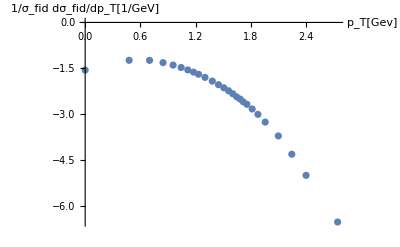

```mathematica
ErrorListPlot[ToPlotB,AxesLabel->{"p_T[Gev]", "1/σ_fid dσ_fid/dp_T[1/GeV]"},PlotRange -> All, LabelStyle->Directive[Black,FontFamily->"Helvetica",10]]
```

```mathematica
dataBExport= Table[formatExport[dataB[[k,i]]]//ToString,{k,1,26},{i,1,4}]
```

{{+1.000000E+00,+2.781000E-02,+1.168020E-04,+1.685433E-04},{+3.000000E+00,+5.802000E-02,+1.508520E-04,+3.040381E-04},{+5.000000E+00,+5.782000E-02,+1.445500E-04,+2.742643E-04},{+7.000000E+00,+4.868000E-02,+1.363040E-04,+2.269240E-04},{+9.000000E+00,+4.047000E-02,+1.254570E-04,+1.835037E-04},{+1.100000E+01,+3.381000E-02,+1.149540E-04,+1.578605E-04},{+1.300000E+01,+2.823000E-02,+1.072740E-04,+1.338769E-04},{+1.500000E+01,+2.385000E-02,+9.540000E-05,+1.113568E-04},{+1.700000E+01,+2.034000E-02,+8.949600E-05,+1.006779E-04},{+2.000000E+01,+1.606000E-02,+6.263400E-05,+7.616234E-05},{+2.400000E+01,+1.217000E-02,+5.719900E-05,+6.195952E-05},{+2.800000E+01,+9.275000E-03,+4.823000E-05,+4.999905E-05},{+3.200000E+01,+7.339000E-03,+4.330010E-05,+4.242044E-05},{+3.600000E+01,+5.880000E-03,+3.880800E-05,+3.540717E-05},{+4.000000E+01,+4.709000E-03,+3.484660E-05,+2.912736E-05},{+4.400000E+01,+3.745000E-03,+3.070900E-05,+2.565530E-05},{+4.800000E+01,+3.156000E-03,+2.714160E-05,+2.278667E-05},{+5.200000E+01,+2.568000E-03,+2.542320E-05,+1.953200E-05},{+5.700000E+01,+2.125000E-03,+1.955000E-05,+1.457756E-05},{+6.500000E+01,+1.494000E-03,+1.299780E-05,+1.119703E-05},{+7.500000E+01,+9.979000E-04,+1.077732E-05,+8.132120E-06},{+9.000000E+01,+5.566000E-04,+5.510340E-06,+4.678421E-06},{+1.250000E+02,+1.974000E-04,+1.974000E-06,+1.968168E-06},{+1.750000E+02,+4.990000E-05,+1.012970E-06,+6.021588E-07},{+2.500000E+02,+1.018000E-05,+3.227060E-07,+2.418152E-07},{+5.500000E+02,+3.048000E-07,+2.444496E-08,+1.161836E-08}}

```mathematica
Export["DY.newATLAS_7TeV_yrap12.list",dataBExport,"table"]
```

DY.newATLAS_7TeV_yrap12.list

## # : ABS (YRAP (Z)), 2.0 - 2.4

```mathematica
tableC=Take[ Import["DY.newATLAS_7TeV.csv","CSV","HeaderLines"->142],26]
```

{{1.,0.,2.,0.0271,1.3,-1.3,1.,-1.,0.5,-0.5},{3.,2.,4.,0.0568,0.8,-0.8,0.7,-0.7,0.4,-0.4},{5.,4.,6.,0.0564,0.8,-0.8,0.5,-0.5,0.5,-0.5},{7.,6.,8.,0.0471,0.8,-0.8,0.6,-0.6,0.5,-0.5},{9.,8.,10.,0.0395,0.9,-0.9,0.6,-0.6,0.4,-0.4},{11.,10.,12.,0.0322,1.,-1.,0.7,-0.7,0.4,-0.4},{13.,12.,14.,0.0266,1.1,-1.1,0.7,-0.7,0.4,-0.4},{15.,14.,16.,0.0227,1.3,-1.3,0.7,-0.7,0.5,-0.5},{17.,16.,18.,0.0199,1.4,-1.4,0.8,-0.8,0.5,-0.5},{20.,18.,22.,0.016,1.2,-1.2,0.6,-0.6,0.5,-0.5},{24.,22.,26.,0.0123,1.4,-1.4,0.8,-0.8,0.6,-0.6},{28.,26.,30.,0.00968,1.7,-1.7,0.8,-0.8,0.6,-0.6},{32.,30.,34.,0.00782,1.8,-1.8,0.9,-0.9,0.5,-0.5},{36.,34.,38.,0.00634,2.,-2.,1.,-1.,0.5,-0.5},{40.,38.,42.,0.00509,2.2,-2.2,1.2,-1.2,0.4,-0.4},{44.,42.,46.,0.00438,2.4,-2.4,1.2,-1.2,0.4,-0.4},{48.,46.,50.,0.00357,2.6,-2.6,1.4,-1.4,0.4,-0.4},{52.,50.,54.,0.003,2.9,-2.9,1.5,-1.5,0.6,-0.6},{57.,54.,60.,0.00266,2.7,-2.7,1.3,-1.3,0.4,-0.4},{65.,60.,70.,0.00182,2.5,-2.5,1.3,-1.3,0.4,-0.4},{75.,70.,80.,0.00114,3.3,-3.3,1.6,-1.6,0.7,-0.7},{90.,80.,100.,0.000596,3.1,-3.1,1.4,-1.4,0.8,-0.8},{125.,100.,150.,0.000198,3.3,-3.3,1.5,-1.5,2.1,-2.1},{175.,150.,200.,0.0000508,6.7,-6.7,2.8,-2.8,2.2,-2.2},{250.,200.,300.,9.09×10^-6,10.9,-10.9,4.4,-4.4,0.8,-0.8},{550.,300.,800.,1.47×10^-7,34.,-34.,15.8,-15.8,0.9,-0.9}}

```mathematica
dataC=(tableC/.{a_,b_,c_,d_,e_,f_,g_,h_,i_,l_}->{a,d,e*d/100,(√((g*d)^2+(i*d)^2))/100})
```

{{1.,0.0271,0.0003523,0.000302987},{3.,0.0568,0.0004544,0.000457936},{5.,0.0564,0.0004512,0.000398808},{7.,0.0471,0.0003768,0.000367863},{9.,0.0395,0.0003555,0.000284839},{11.,0.0322,0.000322,0.000259605},{13.,0.0266,0.0002926,0.000214456},{15.,0.0227,0.0002951,0.000195273},{17.,0.0199,0.0002786,0.000187736},{20.,0.016,0.000192,0.000124964},{24.,0.0123,0.0001722,0.000123},{28.,0.00968,0.00016456,0.0000968},{32.,0.00782,0.00014076,0.0000805118},{36.,0.00634,0.0001268,0.0000708834},{40.,0.00509,0.00011198,0.000064384},{44.,0.00438,0.00010512,0.0000554031},{48.,0.00357,0.00009282,0.00005198},{52.,0.003,0.000087,0.0000484665},{57.,0.00266,0.00007182,0.0000361799},{65.,0.00182,0.0000455,0.0000247547},{75.,0.00114,0.00003762,0.0000199092},{90.,0.000596,0.000018476,9.61021×10^-6},{125.,0.000198,6.534×10^-6,5.10978×10^-6},{175.,0.0000508,3.4036×10^-6,1.80894×10^-6},{250.,9.09×10^-6,9.9081×10^-7,4.06517×10^-7},{550.,1.47×10^-7,4.998×10^-8,2.32636×10^-8}}

```mathematica
ToPlotC=(dataC/.{a_,b_,c_,d_}->{{Log[10,a],Log[10,b]},ErrorBar[{Log[10,(b+√(c^2+d^2))/b]},{Log[10,(b-√(c^2+d^2))/b]}]})
```

{{{0.,-1.56703},ErrorBar[{0.00738348},{-0.00751118}]},{{0.477121,-1.24565},ErrorBar[{0.00490484},{-0.00496086}]},{{0.69897,-1.24872},ErrorBar[{0.00461242},{-0.00466193}]},{{0.845098,-1.32698},ErrorBar[{0.00482862},{-0.00488291}]},{{0.954243,-1.4034},ErrorBar[{0.00497987},{-0.00503763}]},{{1.04139,-1.49214},ErrorBar[{0.00554309},{-0.00561475}]},{{1.11394,-1.57512},ErrorBar[{0.00588296},{-0.00596375}]},{{1.17609,-1.64397},ErrorBar[{0.00671776},{-0.0068233}]},{{1.23045,-1.70115},ErrorBar[{0.00727054},{-0.00739433}]},{{1.30103,-1.79588},ErrorBar[{0.00617406},{-0.0062631}]},{{1.38021,-1.91009},ErrorBar[{0.00740834},{-0.00753691}]},{{1.44716,-2.01412},ErrorBar[{0.00848225},{-0.00865122}]},{{1.50515,-2.10679},ErrorBar[{0.00891362},{-0.00910041}]},{{1.5563,-2.19791},ErrorBar[{0.00983865},{-0.0100667}]},{{1.60206,-2.29328},ErrorBar[{0.0108836},{-0.0111634}]},{{1.64345,-2.35853},ErrorBar[{0.0116251},{-0.0119449}]},{{1.68124,-2.44733},ErrorBar[{0.0127526},{-0.0131384}]},{{1.716,-2.52288},ErrorBar[{0.0141829},{-0.0146617}]},{{1.75587,-2.57512},ErrorBar[{0.0129352},{-0.0133323}]},{{1.81291,-2.73993},ErrorBar[{0.0121876},{-0.0125395}]},{{1.87506,-2.9431},ErrorBar[{0.0159196},{-0.0165254}]},{{1.95424,-3.22475},ErrorBar[{0.0149164},{-0.0154469}]},{{2.09691,-3.70333},ErrorBar[{0.017823},{-0.0185859}]},{{2.24304,-4.29414},ErrorBar[{0.0317618},{-0.0342692}]},{{2.39794,-5.04144},ErrorBar[{0.048371},{-0.0544416}]},{{2.74036,-6.83268},ErrorBar[{0.138311},{-0.204139}]}}

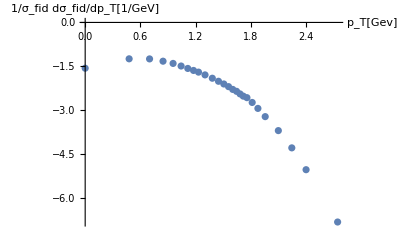

```mathematica
ErrorListPlot[ToPlotC,AxesLabel->{"p_T[Gev]", "1/σ_fid dσ_fid/dp_T[1/GeV]"},PlotRange -> All, LabelStyle->Directive[Black,FontFamily->"Helvetica",10]]
```

```mathematica
dataCExport= Table[formatExport[dataC[[k,i]]]//ToString,{k,1,26},{i,1,4}]
```

{{+1.000000E+00,+2.710000E-02,+3.523000E-04,+3.029872E-04},{+3.000000E+00,+5.680000E-02,+4.544000E-04,+4.579362E-04},{+5.000000E+00,+5.640000E-02,+4.512000E-04,+3.988082E-04},{+7.000000E+00,+4.710000E-02,+3.768000E-04,+3.678628E-04},{+9.000000E+00,+3.950000E-02,+3.555000E-04,+2.848386E-04},{+1.100000E+01,+3.220000E-02,+3.220000E-04,+2.596047E-04},{+1.300000E+01,+2.660000E-02,+2.926000E-04,+2.144561E-04},{+1.500000E+01,+2.270000E-02,+2.951000E-04,+1.952728E-04},{+1.700000E+01,+1.990000E-02,+2.786000E-04,+1.877362E-04},{+2.000000E+01,+1.600000E-02,+1.920000E-04,+1.249640E-04},{+2.400000E+01,+1.230000E-02,+1.722000E-04,+1.230000E-04},{+2.800000E+01,+9.680000E-03,+1.645600E-04,+9.680000E-05},{+3.200000E+01,+7.820000E-03,+1.407600E-04,+8.051183E-05},{+3.600000E+01,+6.340000E-03,+1.268000E-04,+7.088335E-05},{+4.000000E+01,+5.090000E-03,+1.119800E-04,+6.438397E-05},{+4.400000E+01,+4.380000E-03,+1.051200E-04,+5.540310E-05},{+4.800000E+01,+3.570000E-03,+9.282000E-05,+5.197998E-05},{+5.200000E+01,+3.000000E-03,+8.700000E-05,+4.846648E-05},{+5.700000E+01,+2.660000E-03,+7.182000E-05,+3.617991E-05},{+6.500000E+01,+1.820000E-03,+4.550000E-05,+2.475468E-05},{+7.500000E+01,+1.140000E-03,+3.762000E-05,+1.990924E-05},{+9.000000E+01,+5.960000E-04,+1.847600E-05,+9.610211E-06},{+1.250000E+02,+1.980000E-04,+6.534000E-06,+5.109781E-06},{+1.750000E+02,+5.080000E-05,+3.403600E-06,+1.808937E-06},{+2.500000E+02,+9.090000E-06,+9.908100E-07,+4.065172E-07},{+5.500000E+02,+1.470000E-07,+4.998000E-08,+2.326365E-08}}

```mathematica
Export["DY.newATLAS_7TeV_yrap22.4.list",dataCExport,"table"]
```

DY.newATLAS_7TeV_yrap22.4.list

```mathematica
Import["DY.newATLAS_7TeV.csv","Table","HeaderLines"->0];
```